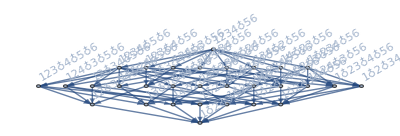
-Graphics-g1234x56

```mathematica
Labeled[FormulaGraphReverse[allGraphs5[allGraphs6GeneratorAtomKeys[[200]],"colofour"]],allGraphs6[allGraphs6GeneratorAtomKeys[[200]],"colofourgenerator"]]
```

```mathematica
Table[Factor[ChromaticPolynomial[allGraphs5[k,"graph"],x]],{k,allGraphs5GeneratorAtomKeys}]//Tally//Sort
```

{{(-4+x) (-3+x) (-2+x) (-1+x) x,1},{(-3+x)^2 (-2+x) (-1+x) x,10},{(-2+x)^3 (-1+x) x,10},{(-1+x)^4 x,5},{x^5,1},{(-2+x) (-1+x) x (7-5 x+x^2),15},{(-1+x) x (-7+10 x-5 x^2+x^3),10}}

```mathematica
Table[Factor[ChromaticPolynomial[allGraphs6[k,"graph"],x]],{k,allGraphs6GeneratorAtomKeys}]//Tally//Sort
```

{{(-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x,1},{(-4+x)^2 (-3+x) (-2+x) (-1+x) x,15},{(-3+x)^3 (-2+x) (-1+x) x,20},{(-2+x)^4 (-1+x) x,15},{(-1+x)^5 x,6},{x^6,1},{(-3+x) (-2+x) (-1+x) x (13-7 x+x^2),45},{(-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),15},{(-2+x) (-1+x) x (-23+23 x-8 x^2+x^3),60},{(-1+x) x (31-47 x+28 x^2-8 x^3+x^4),10},{(-1+x) x (15-29 x+21 x^2-7 x^3+x^4),15}}

```mathematica
TableForm[Map[First,Table[Map[Last,Sort[Tally[Map[SymbolLevel,ListofVars[allGraphs6[k,"colofour"]]]]]],{k,allGraphs6GeneratorAtomKeys}]//Tally//Sort],TableDepth->2]
```

1 |  |  |  |  | 
1 | 1 |  |  |  | 
1 | 2 | 1 |  |  | 
1 | 3 | 1 |  |  | 
1 | 3 | 3 | 1 |  | 
1 | 4 | 4 | 1 |  | 
1 | 7 | 6 | 1 |  | 
1 | 6 | 11 | 6 | 1 | 
1 | 8 | 13 | 7 | 1 | 
1 | 15 | 25 | 10 | 1 | 
1 | 31 | 90 | 65 | 15 | 1

```mathematica
Flatten[Map[First,Table[Map[Last,Sort[Tally[Map[SymbolLevel,ListofVars[allGraphs6[k,"colofour"]]]]]],{k,allGraphs6GeneratorAtomKeys}]//Tally//Sort]]
```

{1,1,1,1,2,1,1,3,1,1,3,3,1,1,4,4,1,1,7,6,1,1,6,11,6,1,1,8,13,7,1,1,15,25,10,1,1,31,90,65,15,1}

```mathematica
TableForm[Sort[Tally[Table[Sort[Tally[Map[SymbolLevel,ListofVars[allGraphs6[k,"colofournull"]]]]],{k,allGraphs6GeneratorAtomKeys}]]],TableDepth->2]
```

{{1,1}} | 1
{{6,1}} | 1
{{1,1},{2,31},{3,90},{4,21}} | 15
{{1,1},{2,31},{3,90},{4,65},{5,15}} | 186

```mathematica
TableForm[Sort[Tally[Table[Sort[Tally[Map[SymbolLevel,ListofVars[allGraphs6[k,"colofourrealnull"]]]]],{k,allGraphs6GeneratorAtomKeys}]]],TableDepth->2]
```

{{6,1}} | 1
{{1,1},{2,5},{3,10},{4,10},{5,5},{6,1}} | 6
{{1,1},{2,20},{3,38},{4,28},{5,8},{6,1}} | 15
{{1,1},{2,20},{3,38},{4,28},{5,9},{6,1}} | 15
{{1,1},{2,24},{3,57},{4,36},{5,9},{6,1}} | 10
{{1,1},{2,26},{3,63},{4,43},{5,11},{6,1}} | 60
{{1,1},{2,27},{3,66},{4,46},{5,12},{6,1}} | 20
{{1,1},{2,28},{3,71},{4,50},{5,12},{6,1}} | 15
{{1,1},{2,29},{3,77},{4,54},{5,13},{6,1}} | 45
{{1,1},{2,30},{3,83},{4,59},{5,14},{6,1}} | 15
{{1,1},{2,31},{3,90},{4,65},{5,15},{6,1}} | 1

```mathematica
TableForm[Sort[Tally[Table[Sort[Map[Last,Tally[Map[SymbolLevel,ListofVars[allGraphs6[k,"colofourgenerator"]]]]]],{k,allGraphs6FakeAtomKeys}]]],TableDepth->2]
```

{1} | 2
{1,5} | 6
{1,6,9} | 10
{1,8,12} | 15
{1,9,16} | 15
{1,11,18,30} | 60
{1,12,27,37} | 20
{1,4,8,12,30} | 15
{1,8,9,10,18} | 45
{1,14,16,55,65} | 15

```mathematica
TableForm[Sort[Tally[Table[Sort[Map[Last,Tally[Map[SymbolLevel,ListofVars[allGraphs6[k,"colofour"]]]]]],{k,allGraphs6GeneratorAtomKeys}]]],TableDepth->2]
```

{1} | 1
{1,1} | 15
{1,1,2} | 45
{1,1,3} | 20
{1,1,3,3} | 15
{1,1,4,4} | 60
{1,1,6,7} | 15
{1,1,6,6,11} | 10
{1,1,7,8,13} | 15
{1,1,10,15,25} | 6
{1,1,15,31,65,90} | 1

```mathematica
TableForm[Sort[Tally[Table[Sort[Map[Last,Tally[Map[SymbolLevel,ListofVars[allGraphs6[k,"colofourrealnull"]]]]]],{k,allGraphs6GeneratorAtomKeys}]]],TableDepth->2]
```

{1} | 1
{1,1,5,5,10,10} | 6
{1,1,8,20,28,38} | 15
{1,1,9,20,28,38} | 15
{1,1,9,24,36,57} | 10
{1,1,11,26,43,63} | 60
{1,1,12,27,46,66} | 20
{1,1,12,28,50,71} | 15
{1,1,13,29,54,77} | 45
{1,1,14,30,59,83} | 15
{1,1,15,31,65,90} | 1